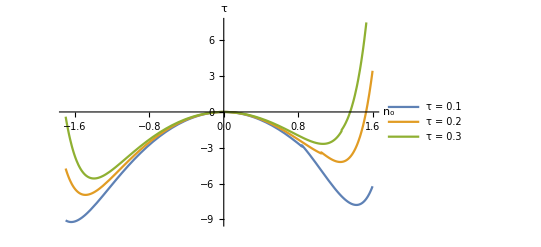

.png

```mathematica
FvdW = τ*(no + 1)* Log[((no + 1)*(1 - b))/(1 - (no + 1)*b)]- a1*no^2 - τ/(1 - b) * no;
FvdWexpansion =Normal[Series[FvdW,{no, 0.0, 10}]];
Fex =-Bx*τ*Exp[-τ/Tm]*3*(ϕ)^2 + d/2* no^2 ; (*???*)
Fzeta1 = a2/2 (6 ϕ^2);
Fzeta2 = a3/3 (18*no*ϕ^2+12*ϕ^3);
Fzeta3 = a4/4(36*no^2*ϕ^2+48*no*ϕ^3+90*ϕ^4);
F = FvdWexpansion+Fex +  Fzeta1 + Fzeta2 + Fzeta3;

nmin = -1.25;(*-1.5;*)
nmax = 1.2;(*2.0;*) 
Fsubs = F/.{ a1-> 4.65, b-> 0.5, a2 -> 2.0+6* τ+0.17* τ^2, a3-> -1.2-0.6* τ+0.14* τ^2, a4 -> 0.11, Bx -> 1.5, Tm -> 1.0, d ->0.0(*3.3*τ*)};
Ffcc[n0_, T_]:=FindMinimum[{Fsubs/.{ no->n0,τ -> T}, {ϕ} ∈ Reals, ϕ≥ 0
}, {ϕ, 1.0}][[1]];
Fl[n0_, T_] := Fsubs/.{ϕ -> 0, no->n0, τ -> T}; 
plottingT = 0.2;
p1 = Show[Plot[{ Ffcc[nn,0.1], Ffcc[nn,0.2],  Ffcc[nn,0.3]}, {nn, -1.7, 1.6}, PlotLegends->{Style["τ = 0.1" ,Black,Bold,14],Style["τ = 0.2" ,Black,Bold,14],Style["τ = 0.3" ,Black,Bold,14]},AxesLabel->{Style["n_o",Black, FontSize->18], Style["τ",Black, FontSize-> 18]}, TicksStyle->Directive[Black, 12]]]
Export[".png",p1]
```

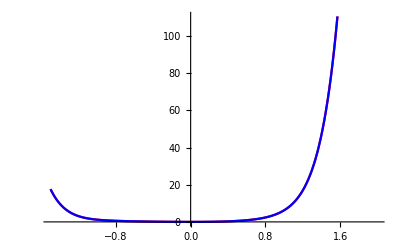

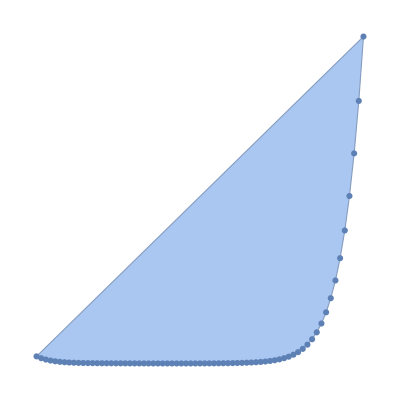

-Graphics3D-

```mathematica
nStep = 0.05;
nmax = 2.0;
Show[Plot[{Fl[nn, plottingT],Ffcc[nn, plottingT]}, {nn, nmin, nmax}, PlotStyle->{Red, Blue}]]

fcn=Table[{i,Ffcc[i, plottingT]},{i,nmin,nmax,nStep}]  ;
convHull = ConvexHullMesh[fcn];
Show[convHull,ListPlot[fcn],AspectRatio->1]

G[n0_, T_] := FindMinimum[{Fsubs/.{ no->n0,τ -> T}, {ϕ} ∈ Reals, ϕ≥ 0
}, {ϕ, 1.0}][[2]];

Show[Plot3D[ϕ/.G[nn, T], {nn, nmin, nmax}, {T, 0.01, 1.0}, AxesLabel->{ "no", "τ", "ϕ"}]]
```

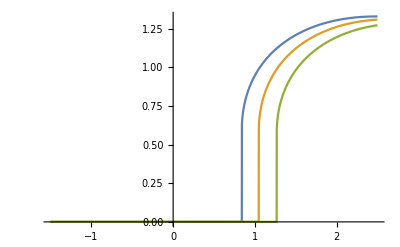

```mathematica
Show[Plot[{ϕ/.G[nn, 0.1], ϕ/.G[nn, 0.2], ϕ/.G[nn, 0.3]}, {nn, -1.5, 2.5} ]]
```

```mathematica
0.8*0.25
```

```mathematica
D[Normal[Series[τ*(no + 1)* Log[((no + 1)*(1 - b))/(1 - (no + 1)*b)]- a1*no^2 - τ/(1 - b) * no, {no, 0, 10}]], no]/.{b-> 0.5}
```

```mathematica
bval = 0.5;
aval = 3.1*(1 - 0.8*no)
b2 = τ/(bval - 1)^2 - 2*aval;
b3 = τ* (1 - 3 * bval)/(6 * (bval - 1)^3);
b4 = τ * (1 - 4 * bval + 6 * bval^2)/(12 * (bval - 1)^4)
```

3.1 (1-0.8 no)

```mathematica
G[n0_, T_] := FindMinimum[{Fsubs/.{ no->n0,τ -> T}, {ϕ} ∈ Reals, ϕ≥ 0
}, {ϕ, 1.0}][[2]];
G[0,0.2]
```

{ϕ→0.000132084}

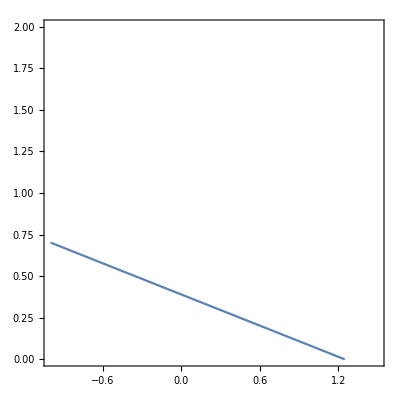

```mathematica
d1 = ContourPlot[b2/2+ b3 + b4 + 1.815873015873016* τ + 2.8 * τ == 0,{no, -1, 1.5}, {τ, 0.0, 2.0}];
Show[d1]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

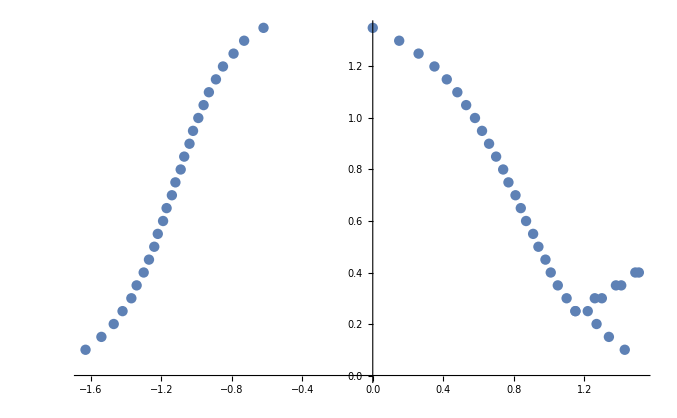

```mathematica
commonTangent = {};
spinodal = {};
convexStep = 0.01;
For[T= 0.1, T< 1.5, T = T + 0.05, 
	fcn=Table[{i,Ffcc[i, T]},{i,nmin,nmax,convexStep}]  ;
	b = Interpolation[fcn, Method-> "Spline"];
	spin = b'';
	s1=x/.FindRoot[spin[x]==0,{x,-0.7}];
	s2=x/.FindRoot[spin[x]==0,{x,0.2}];
	s3=x/.FindRoot[spin[x]==0,{x,0.7}];
	convHull = ConvexHullMesh[fcn];
	convHulln = MeshCoordinates[convHull][[All, 1]];

	len = Length[convHulln];
	dummy = {};

	For[i =  len, i>2, i--,
	If[Abs[convHulln[[i]] -(convHulln[[i - 1]] )]- convexStep>0.000001  ,
	dummy = Append[dummy, {convHulln[[i]], convHulln[[i - 1]]}]
	]
	];
	
	For[ j = 1, j <= Length[dummy], j++,
	commonTangent = Append[commonTangent, {dummy[[j,1]], T}];
	commonTangent = Append[commonTangent, {dummy[[j,2]], T}];
	];
If[T<2.0,
If[Abs[s1] > 0.0001, 
spinodal=Append[spinodal,{s1,T}];
];
If[Abs[s2] > 0.0001,
spinodal=Append[spinodal,{s2,T}];
];
If[Abs[s3] > 0.0001,
spinodal=Append[spinodal,{s3,T}];
];
];

];
ListPlot[commonTangent]
```

```mathematica
GoldData = {{0.16574585635359096,5.316041753106369},
{0.38674033149171194,5.967997292162557},
{0.7458563535911598,6.48147642652807},
{1.2707182320441985,6.9157403970039075},
{1.8508287292817673,7.211609853034306},
{2.486187845303868,7.408610486318869},
{3.3701657458563528,7.60536544886773},
{4.613259668508288,7.722714170288034},
{5.662983425414366,7.721676893848404},
{6.4364640883977895,7.7011497390430845},
{7.237569060773481,7.601543904090144},
{7.955801104972377,7.482257113532635},
{8.867403314917127,7.303490708186839},
{9.751381215469612,7.085225907889852},
{10.80110497237569,6.688931714454173},
{11.740331491712709,6.29274670801214},
{12.348066298342541,5.995703491800056},
{12.955801104972377,5.659134583888367},
{13.97790055248619,4.887373616054854},
{14.447513812154696,4.511415500185616},
{14.917127071823206,4.076168846766972},
{15.331491712707184,3.6805024785447538},
{15.718232044198896,3.225574869521541},
{16.132596685082873,2.770619963749919},
{16.49171270718232,2.2959568056253126},
{16.87845303867403,1.8015035049024934},
{17.12707182320442,1.4455266088703507},
{17.34806629834254,1.168628392985827},
{17.734806629834253,1.286823313606881},
{18.12154696132597,1.444543925927542},
{18.50828729281768,1.5825016923984006},
{18.97790055248619,1.7599032603236289},
{19.41988950276243,1.917569279147468},
{20,2.094861660079051},
{20.607734806629836,2.2721267442622217},
{20.966850828729285,2.3705861157818866},
{20.966850828729285,2.271771886532875},
{20.635359116022098,2.1732852182648},
{20,1.9762845849802364},
{19.41988950276243,1.7792293581988492},
{19.005524861878452,1.601773196776799},
{18.50828729281768,1.325584696350969},
{18.28729281767956,1.1479374576900394},
{18.50828729281768,0.9303277793549221},
{18.812154696132595,0.6335848273753619},
{19.03314917127072,0.37644945734064095},
{19.25414364640884,0.1390769331557209},
{18.7292817679558,1.443943397462494},
{19.143646408839782,1.641162404734347},
{19.530386740331494,1.818645862904809},
{19.751381215469614,1.877716026466926}};
```

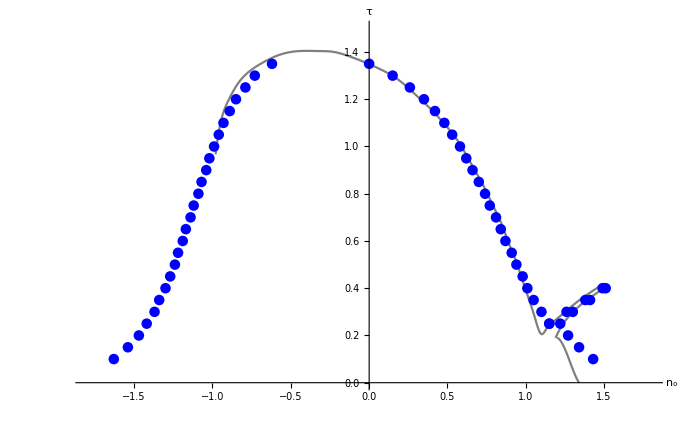

```mathematica
Gold1 = {{0.16574585635359096,5.316041753106369},
{0.38674033149171194,5.967997292162557},
{0.7458563535911598,6.48147642652807},
{1.2707182320441985,6.9157403970039075},
{1.8508287292817673,7.211609853034306},
{2.486187845303868,7.408610486318869},
{3.3701657458563528,7.60536544886773},
{4.613259668508288,7.722714170288034},
{5.662983425414366,7.721676893848404},
{6.4364640883977895,7.7011497390430845},
{7.237569060773481,7.601543904090144},
{7.955801104972377,7.482257113532635},
{8.867403314917127,7.303490708186839},
{9.751381215469612,7.085225907889852},
{10.80110497237569,6.688931714454173},
{11.740331491712709,6.29274670801214},
{12.348066298342541,5.995703491800056},
{12.955801104972377,5.659134583888367},
{13.97790055248619,4.887373616054854},
{14.447513812154696,4.511415500185616},
{14.917127071823206,4.076168846766972},
{15.331491712707184,3.6805024785447538},
{15.718232044198896,3.225574869521541},
{16.132596685082873,2.770619963749919},
{16.49171270718232,2.2959568056253126},
{16.87845303867403,1.8015035049024934},
{17.12707182320442,1.4455266088703507},
{17.34806629834254,1.168628392985827},
{17.734806629834253,1.286823313606881},
{18.12154696132597,1.444543925927542},
{18.50828729281768,1.5825016923984006},
{18.97790055248619,1.7599032603236289},
{19.41988950276243,1.917569279147468},
{20,2.094861660079051},
{20.607734806629836,2.2721267442622217},
{20.966850828729285,2.3705861157818866}};
Gold2 = 
{{20.966850828729285,2.271771886532875},
{20.635359116022098,2.1732852182648},
{20,1.9762845849802364},
{19.41988950276243,1.7792293581988492},
{19.005524861878452,1.601773196776799},
{18.50828729281768,1.325584696350969},
{18.28729281767956,1.1479374576900394}};

Gold3 = {{18.50828729281768,0.9303277793549221},
{18.812154696132595,0.6335848273753619},
{19.03314917127072,0.37644945734064095},
{19.25414364640884,0.1390769331557209}};

rhoBar = 8.3;
T0 = 5.5;
Do[	
	Gold1[[i,1]] = (Gold1[[i,1]] - rhoBar )/rhoBar;
	Gold1[[i,2]] = Gold1[[i,2]] /T0 ;(*fit the temperature data*),
{i, 1, Length[Gold1]}
]
Do[	
	Gold2[[i,1]] = (Gold2[[i,1]] - rhoBar )/rhoBar;
	Gold2[[i,2]] = Gold2[[i,2]] /T0  ;(*fit the temperature data*),
{i, 1, Length[Gold2]}
]
Do[	
	Gold3[[i,1]] = (Gold3[[i,1]] - rhoBar )/rhoBar;
	Gold3[[i,2]] = Gold3[[i,2]] /T0 ;(*fit the temperature data*),
{i, 1, Length[Gold3]}
]

A= Interpolation[Gold1, Method-> "Spline"];
B = Interpolation[Gold2, Method-> "Spline"];
H = Interpolation[Gold3, Method -> "Spline"];

g1 = Plot[A[x], {x, -0.98, 1.5}, PlotStyle->Gray,  PlotRange->{{-1.8, 1.8
}, {0, 1.5}}, AxesLabel->{Style["n_o",Black, FontSize->30], Style["τ",Black, FontSize-> 30]}, TicksStyle->Directive[Black, 18]];
g2 = Plot[B[x], {x, 1.19, 1.5}, PlotStyle->Gray];
g3 = Plot[H[x], {x, 1.2, 1.34}, PlotStyle-> Gray];
g4 =ListPlot[Gold1, PlotStyle->Gray];
g5 = ListPlot[Gold2, PlotStyle->Gray];
g6 = ListPlot[Gold3, PlotStyle-> Gray];
p1 = ListPlot[commonTangent, PlotStyle -> Blue];
Show[ g1, g2, g3, p1]
```

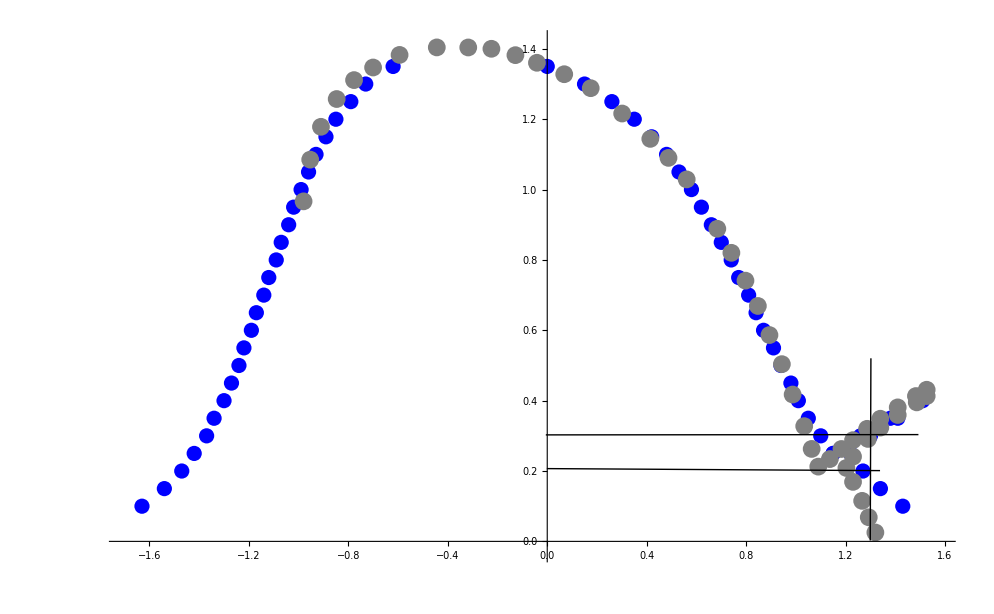

-Graphics-

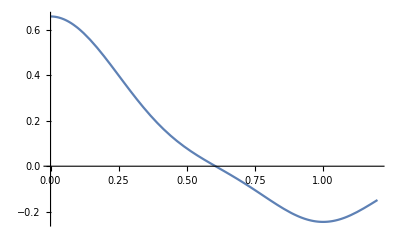

```mathematica
corr := -tau * Bx * Exp[-tau/Tm]*Exp[-1/(2*alpha^2)* (k - qo)^2] + d * tau * Exp[-k^2/(2 * beta^2)];
linear :=-tau*Bx*Exp[-tau]+(1/(2*alpha*alpha))*Bx*tau*Exp[-tau]*(k-qo)*(k-qo);
Plot[{ corr/.{tau -> 0.2, Tm-> 1, Bx -> 1.5, alpha -> 0.2, beta-> 0.25, qo -> 1, d -> 3.3}}, {k, 0, 1.2}]
```

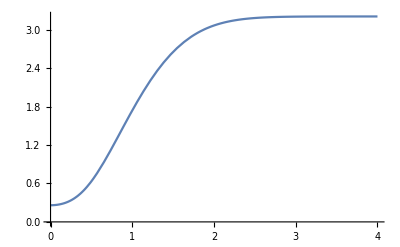

```mathematica
Plot[ 1.3* tau*Exp[-k^2/(2 * beta^2)]  +  (2.0+6* tau+0.17* tau^2)*(1 -  ( Exp[-  k^2/(2 * lambda * lambda)]))-tau * Bx * Exp[-tau/Tm]*Exp[-1/(2*alpha^2)* (k - qo)^2]   /.{tau -> 0.2, Tm-> 1, Bx -> 0.0, alpha -> 0.2, beta-> 0.3, lambda -> 0.8,qo -> 1, d -> 3.3, a1 ->  4.65 , b-> 0.5}, {k, 0, 4}]
```

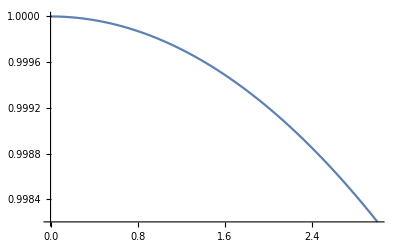

```mathematica
Plot[ (  (  Exp[-  (k )^2/(2 * 50^2)])  )/.{tau -> 0.3, Tm-> 1, Bx -> 1.5, alpha -> 0.4, beta-> 0.5, lambda -> 0.5,qo -> 2*Pi/Sqrt[3], d -> 3.8, a1 ->  4.65 , b-> 0.5}, {k, 0, 3}]
```

```mathematica
2*Pi/Sqrt[3.]
```

3.6276

```mathematica
1.3 * 0.25 + (-1.4)*0.75
```

-0.725

```mathematica
1 - 1.45/3
```

0.516667

```mathematica
2.125/3
```

0.708333

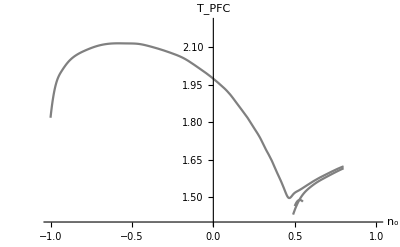

```mathematica
Gold1 = {{0.16574585635359096,5.316041753106369},
{0.38674033149171194,5.967997292162557},
{0.7458563535911598,6.48147642652807},
{1.2707182320441985,6.9157403970039075},
{1.8508287292817673,7.211609853034306},
{2.486187845303868,7.408610486318869},
{3.3701657458563528,7.60536544886773},
{4.613259668508288,7.722714170288034},
{5.662983425414366,7.721676893848404},
{6.4364640883977895,7.7011497390430845},
{7.237569060773481,7.601543904090144},
{7.955801104972377,7.482257113532635},
{8.867403314917127,7.303490708186839},
{9.751381215469612,7.085225907889852},
{10.80110497237569,6.688931714454173},
{11.740331491712709,6.29274670801214},
{12.348066298342541,5.995703491800056},
{12.955801104972377,5.659134583888367},
{13.97790055248619,4.887373616054854},
{14.447513812154696,4.511415500185616},
{14.917127071823206,4.076168846766972},
{15.331491712707184,3.6805024785447538},
{15.718232044198896,3.225574869521541},
{16.132596685082873,2.770619963749919},
{16.49171270718232,2.2959568056253126},
{16.87845303867403,1.8015035049024934},
{17.12707182320442,1.4455266088703507},
{17.34806629834254,1.168628392985827},
{17.734806629834253,1.286823313606881},
{18.12154696132597,1.444543925927542},
{18.50828729281768,1.5825016923984006},
{18.97790055248619,1.7599032603236289},
{19.41988950276243,1.917569279147468},
{20,2.094861660079051},
{20.607734806629836,2.2721267442622217},
{20.966850828729285,2.3705861157818866}};
Gold2 = 
{{20.966850828729285,2.271771886532875},
{20.635359116022098,2.1732852182648},
{20,1.9762845849802364},
{19.41988950276243,1.7792293581988492},
{19.005524861878452,1.601773196776799},
{18.50828729281768,1.325584696350969},
{18.28729281767956,1.1479374576900394}};

Gold3 = {{18.50828729281768,0.9303277793549221},
{18.812154696132595,0.6335848273753619},
{19.03314917127072,0.37644945734064095},
{19.25414364640884,0.1390769331557209}};

rhoBar = 11.9;
T0 = 0.094;
Tshift = 1.39;
Do[	
	Gold1[[i,1]] = (Gold1[[i,1]] - rhoBar )/rhoBar;
	Gold1[[i,2]] = Gold1[[i,2]] *T0 + Tshift ;(*fit the temperature data*),
{i, 1, Length[Gold1]}
]
Do[	
	Gold2[[i,1]] = (Gold2[[i,1]] - rhoBar )/rhoBar;
	Gold2[[i,2]] = Gold2[[i,2]] *T0 + Tshift ;(*fit the temperature data*),
{i, 1, Length[Gold2]}
]
Do[	
	Gold3[[i,1]] = (Gold3[[i,1]] - rhoBar )/rhoBar;
	Gold3[[i,2]] = Gold3[[i,2]] *T0 + Tshift ;(*fit the temperature data*),
{i, 1, Length[Gold3]}
]

A= Interpolation[Gold1, Method-> "Spline"];
B = Interpolation[Gold2, Method-> "Spline"];
H = Interpolation[Gold3, Method -> "Spline"];

g1 = Plot[A[x], {x, -1, 0.8}, PlotStyle->Gray,  PlotRange->{{-1, 1
}, {1.4, 2.2}}, AxesLabel->{"n_o", "T_PFC"}];
g2 = Plot[B[x], {x, 0.49, 0.8}, PlotStyle->Gray];
g3 = Plot[H[x], {x, 0.5, 0.55}, PlotStyle-> Gray];
g4 =ListPlot[Gold1, PlotStyle->Gray];
g5 = ListPlot[Gold2, PlotStyle->Blue];
g6 = ListPlot[Gold3, PlotStyle-> Red];
Show[ g1, g2, g3]
```